# Stochastic Hill Climbers

## Jovana Andrejevic, Nina Andrejevic, and George Varnavides

## Workshop Teaser

We’ll code the workshop teaser!
The idea is simple:

Start with 50 8-vertex polygons randomly in space

Assign a color and transparency to each polygon

Randomly nudge one of the vertices

If resulting image is closer to the target image, accept change, otherwise reject

Iterate until convergence

```mathematica
obama=ImageResize[Import["https://www.beyonddream.com/images/product/23892024.jpg"],500]
```

-Graphics-

```mathematica
QuaCol[i_,n_]:=RGBColor/@Union[Flatten[ImageData[ColorQuantize[i,n]],1]]
```

Find the 50 ‘dominant’ colors

```mathematica
colors=Sort[QuaCol[obama,50]]
```

{RGBColor[{0.06274509803921569, 0.4, 0.4}],RGBColor[{0.08627450980392157, 0.2549019607843137, 0.24313725490196078}],RGBColor[{0.08627450980392157, 0.5372549019607843, 0.5254901960784314}],RGBColor[{0.10196078431372549, 0.13333333333333333, 0.11764705882352941}],RGBColor[{0.12549019607843137, 0.796078431372549, 0.792156862745098}],RGBColor[{0.15294117647058825, 0.17254901960784313, 0.1568627450980392}],RGBColor[{0.1803921568627451, 0.8235294117647058, 0.8352941176470589}],RGBColor[{0.18823529411764706, 0.43137254901960786, 0.44313725490196076}],RGBColor[{0.2, 0.24705882352941178, 0.23137254901960785}],RGBColor[{0.20784313725490197, 0.596078431372549, 0.592156862745098}],RGBColor[{0.2235294117647059, 0.3215686274509804, 0.33725490196078434}],RGBColor[{0.2235294117647059, 0.7843137254901961, 0.7725490196078432}],RGBColor[{0.28627450980392155, 0.32941176470588235, 0.34509803921568627}],RGBColor[{0.3176470588235294, 0.2823529411764706, 0.26666666666666666}],RGBColor[{0.3254901960784314, 0.38823529411764707, 0.40784313725490196}],RGBColor[{0.35294117647058826, 0.1803921568627451, 0.14901960784313725}],RGBColor[{0.35294117647058826, 0.21568627450980393, 0.21176470588235294}],RGBColor[{0.35294117647058826, 0.8313725490196079, 0.8549019607843137}],RGBColor[{0.36470588235294116, 0.43529411764705883, 0.4745098039215686}],RGBColor[{0.36470588235294116, 0.803921568627451, 0.788235294117647}],RGBColor[{0.38823529411764707, 0.7686274509803922, 0.8196078431372549}],RGBColor[{0.39215686274509803, 0.7411764705882353, 0.7411764705882353}],RGBColor[{0.4117647058823529, 0.5882352941176471, 0.5882352941176471}],RGBColor[{0.41568627450980394, 0.6784313725490196, 0.6431372549019608}],RGBColor[{0.42745098039215684, 0.5333333333333333, 0.49411764705882355}],RGBColor[{0.5568627450980392, 0.20784313725490197, 0.18823529411764706}],RGBColor[{0.5607843137254902, 0.5294117647058824, 0.4980392156862745}],RGBColor[{0.5686274509803921, 0.43529411764705883, 0.4235294117647059}],RGBColor[{0.5725490196078431, 0.6274509803921569, 0.6196078431372549}],RGBColor[{0.5725490196078431, 0.7647058823529411, 0.7607843137254902}],RGBColor[{0.6, 0.5450980392156862, 0.5647058823529412}],RGBColor[{0.611764705882353, 0.9098039215686274, 0.9254901960784314}],RGBColor[{0.615686274509804, 0.8274509803921568, 0.8745098039215686}],RGBColor[{0.6235294117647059, 0.6823529411764706, 0.7058823529411765}],RGBColor[{0.6352941176470588, 0.27450980392156865, 0.24313725490196078}],RGBColor[{0.6470588235294118, 0.3254901960784314, 0.3215686274509804}],RGBColor[{0.6823529411764706, 0.4392156862745098, 0.4196078431372549}],RGBColor[{0.6980392156862745, 0.2, 0.17647058823529413}],RGBColor[{0.8117647058823529, 0.27058823529411763, 0.23529411764705882}],RGBColor[{0.8196078431372549, 0.4470588235294118, 0.44313725490196076}],RGBColor[{0.8431372549019608, 0.6823529411764706, 0.7215686274509804}],RGBColor[{0.8588235294117647, 0.7647058823529411, 0.7764705882352941}],RGBColor[{0.8705882352941177, 0.396078431372549, 0.3568627450980392}],RGBColor[{0.8862745098039215, 0.5568627450980392, 0.5607843137254902}],RGBColor[{0.8941176470588236, 0.3254901960784314, 0.3058823529411765}],RGBColor[{0.9490196078431372, 0.27450980392156865, 0.23529411764705882}],RGBColor[{0.9490196078431372, 0.5450980392156862, 0.5176470588235295}],RGBColor[{0.9607843137254902, 0.8588235294117647, 0.9215686274509803}],RGBColor[{0.9686274509803922, 0.8862745098039215, 0.9294117647058824}],RGBColor[{0.9725490196078431, 0.6313725490196078, 0.611764705882353}]}

```mathematica
pixelPts=Tuples[Range[1,#,3]&/@ImageDimensions[obama]];
```

```mathematica
polygon[integers_,col_]:=Block[{order=First@FindCurvePath[pixelPts[[integers]]]},
{Opacity[0.5],col,Polygon[integers[[order]]]}]
```

Make a random polygon

{Opacity[0.5],RGBColor[1, 0, 0],Polygon[{18387,19398,22315,19398,12899,3991,3484,11421,18387}]}

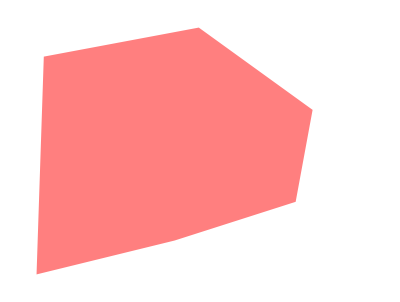

```mathematica
polygon[RandomChoice[Range[Length[pixelPts]],8],Red]
Graphics[GraphicsComplex[pixelPts,%]]
```

Make visualization function

```mathematica
rasterize[dna_,cols_:colors]:=Rasterize[Graphics[GraphicsComplex[pixelPts,MapThread[polygon,{Partition[dna,8],cols}]],ImageSize->500,PlotRange->{{1,500},{1,417}}]]
```

Make a collection of random polygons

```mathematica
rasterize[RandomSample[Range[Length[pixelPts]],50 8]]
```

-Graphics-

```mathematica
imageDistance[string_]:=ImageDistance[obama,rasterize[string],DistanceFunction->SquaredEuclideanDistance]
```

Compute the distance metric

```mathematica
imageDistance[RandomSample[Range[Length[pixelPts]],50 8]]
```

86980.7

‘Mutate’ by randomly ‘nudging’ a corner

```mathematica
mutate[m_][dna_]:=Block[{neighs=RandomInteger[{1,Length[dna]},m]},
ReplacePart[dna,Thread[neighs->RandomSample[Range[Length[pixelPts]],m]]]]
```

Accept/reject ‘mutation’ and ‘evolve’

```mathematica
iterate[m_]:=Block[{mutation,metric,result},
mutation=mutate[m][dna];
metric=imageDistance[mutation];
result=If[metric<previous,
previous=metric;
mutation,dna];
n++;
result]
```

```mathematica
n=0;
dna=RandomSample[Range[Length[pixelPts]],50 8];
og=previous=imageDistance[dna]
```

104595.

Let’s watch the evolution dynamically

```mathematica
Dynamic[Show[rasterize[dna],PlotLabel->Style[StringTemplate["Scaled Image Distance: `1`"][previous/og],24,Black]]]
```

```mathematica
Do[dna=iterate[1];
Pause[0.01],{1000000}]
```

$Aborted